```mathematica
λ2=0.2573
```

0.2573

```mathematica
A3[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
AS3[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
T3[zh_]:=1/(π zh)
```

```mathematica
g3[z_,zh_]:=1-(1/zh^4) z^4
```

```mathematica
a03[zh_]:=NIntegrate[(z^2*Exp[-2*AS3[z]])/(√(g3[z,zh](1-g3[z,zh]))),{z,0,zh}]
```

```mathematica
q3[zh_]:=λ2/(Pi*a03[zh])
```

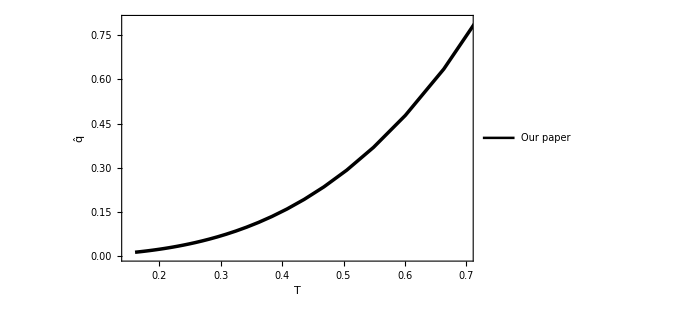

```mathematica
x3=ListLinePlot[ParallelTable[{Re[T3[zh]],Re[q3[zh]]},{zh,0.03,2,0.05}],Frame->True,PlotStyle->{{Black,Thickness[0.005]}},BaseStyle->{Black,FontSize->17},PlotLegends->Placed[LineLegend[{"Our paper"},LabelStyle->{FontSize->15}],{0.8,0.8}],FrameLabel->{Style["T",15,Black,Italic],Style[Overscript["q","^"],15,Black,Italic]},PlotRange->{{0.15,0.7},{0,0.8}} ,ImageSize->{500,300}]
```

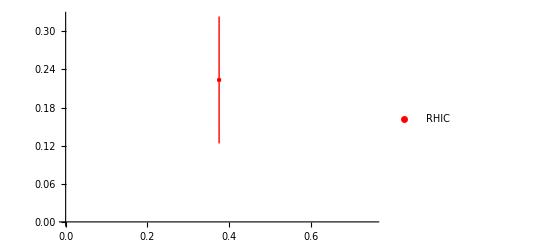

```mathematica
pointWithYErrorBar1=ListPlot[{{0.374992,Around[0.22349,0.1]}},(*仅在 y 轴上设置误差*)PlotStyle->{Red,PointSize[Large]} ,PlotLegends->Placed[LineLegend[{"RHIC"},LabelStyle->{FontSize->15}],{0.8,0.8}](*样式设置*)]
```

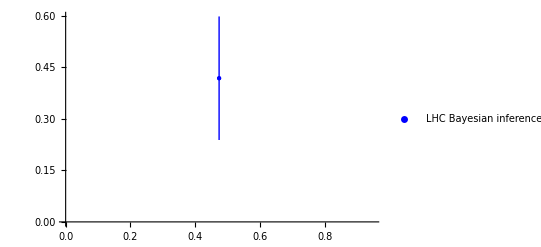

```mathematica
pointWithYErrorBar2=ListPlot[{{0.473318,Around[0.418727,0.18]}},(*仅在 y 轴上设置误差*)PlotStyle->{Blue,PointSize[Large]} ,PlotLegends->Placed[LineLegend[{"LHC Bayesian inference"},LabelStyle->{FontSize->15}],{0.8,0.8}](*样式设置*)]
```

```mathematica
combinedPlot=Show[x3,pointWithYErrorBar1,pointWithYErrorBar2,Frame->True,BaseStyle->{FontFamily->"Times New Roman",FontSize->16},FrameLabel->{Style["T",16,Black,Italic,FontFamily->"Times New Roman"],Style[q̂,16,Black,FontFamily->"Times New Roman"]},FrameStyle->Directive[FontFamily->"Times New Roman",FontSize->16],PlotLegends->Placed[LineLegend[{"x3","pointWithYErrorBar1","pointWithYErrorBar2"},LabelStyle->{FontSize->16}],{0.8,0.8}],ImageSize->{500,300}]
```